# Old 3D Footed Simulation Model with Reduction using MEX

## Initialization

```mathematica
dl1=DateString[]
```

Thu 27 Mar 2014 09:26:01

```mathematica
nbdir=NotebookDirectory[]
```

/home/rsinnet/Documents/MATLAB/kneefoot3d-sva-v33/

```mathematica
snakeyamldir=FileNameJoin[{nbdir,"third","snakeyaml"}];
utildir=FileNameJoin[{nbdir,"util"}];
screwsdir=FileNameJoin[{nbdir,"third","Screws"}];
```

```mathematica
$Path = DeleteDuplicates[Join[$Path,{utildir,snakeyamldir,screwsdir}]]
```

{/usr/local/Wolfram/Mathematica/8.0/SystemFiles/Links,/home/rsinnet/.Mathematica/Kernel,/home/rsinnet/.Mathematica/Autoload,/home/rsinnet/.Mathematica/Applications,/usr/share/Mathematica/Kernel,/usr/share/Mathematica/Autoload,/usr/share/Mathematica/Applications,.,/home/rsinnet,/usr/local/Wolfram/Mathematica/8.0/AddOns/Packages,/usr/local/Wolfram/Mathematica/8.0/AddOns/LegacyPackages,/usr/local/Wolfram/Mathematica/8.0/SystemFiles/Autoload,/usr/local/Wolfram/Mathematica/8.0/AddOns/Autoload,/usr/local/Wolfram/Mathematica/8.0/AddOns/Applications,/usr/local/Wolfram/Mathematica/8.0/AddOns/ExtraPackages,/usr/local/Wolfram/Mathematica/8.0/SystemFiles/Kernel/Packages,/usr/local/Wolfram/Mathematica/8.0/Documentation/English/System,/home/rsinnet/Documents/MATLAB/kneefoot3d-sva-v33/util,/home/rsinnet/Documents/MATLAB/kneefoot3d-sva-v33/third/snakeyaml,/home/rsinnet/Documents/MATLAB/kneefoot3d-sva-v33/third/Screws}

```mathematica
Needs["RobotLinks`"]
```

```mathematica
Needs["SnakeYaml`"]
SnakeYaml`YamlInit[FileNameJoin[{snakeyamldir,"snakeyaml-1.10.jar"}]]
```

Yaml already initizialized

```mathematica
builddir=FileNameJoin[{nbdir,"build_"<>FileBaseName[NotebookFileName[]]}]
```

/home/rsinnet/Documents/MATLAB/kneefoot3d-sva-v33/build_old-model-2d-point-feet-amber-suite

```mathematica
If[DirectoryQ[builddir],,CreateDirectory[builddir]];
```

Dimension of the space in which the robot operates

```mathematica
dim=2;
```

```mathematica
constsubs={
Lft->1/4, (* foot ankle–toe length *)
Lfh->(1 1)/(4 4), (* foot ankle–heel length *)
ha->(1 1)/(5 2),(* height of ankle *)
Lc->0.50,(* calf length *)
Lt->0.50,(* thigh length *)
rfx->-(2 1)/(3 6),(* foot CoM x *)
rfz->(2 1 1)/(3 3 6),(* foot CoM z *)
rcx->0,(* calf CoM x *)
rcz->0.375,(* calf CoM z *)
rtx->0,(* thigh CoM x *)
rtz->0.175,(* thigh CoM z *)
rTx->0, (* torso CoM x *)
rTz->0.075,(* torso CoM z *)
wHip->0.25 p[1],
wFoot->0.08p[1],
mf->0.1,
mc->1.5,
mt->5,
mT->20,
g->9.81
}//Rationalize
```

{Lft→1/4,Lfh→1/16,ha→1/10,Lc→1/2,Lt→1/2,rfx→-1/9,rfz→1/27,rcx→0,rcz→3/8,rtx→0,rtz→7/40,rTx→0,rTz→3/40,wHip→(p(1))/4,wFoot→(2 p(1))/25,mf→1/10,mc→3/2,mt→5,mT→20,g→981/100}

```mathematica
np=1;(* Number of parameters that can be passed in p arugment. *)
```

#### State space

```mathematica
Qb={Subscript[p, x][t],Subscript[p, z][t],Subscript[q, y][t]};
dQb=D[Qb, t];
Xb=Join[Qb,dQb];
nb=Length[Qb];
```

```mathematica
nr=4;
Qr=(Subscript[q, #1][t]&)/@Range[nr]
dQr=D[Qr, t];
Xr=Join[Qr,dQr];
```

{q_1(t),q_2(t),q_3(t),q_4(t)}

```mathematica
nl=nr+1; (* Number of rigid links. *)
```

```mathematica
Q=Join[Qb,Qr];
dQ=Join[dQb,dQr];
X=Join[Q,dQ];
ne=Length[Q];
```

#### Subs for absolute coordinates

MATLAB shall pass the absolute coordinates as though they were relative coordinates according to this substitution list. It is a trivial pattern replacement.

```mathematica
ζxsubs=((Qr⟦#⟧/.q->ζ)->Qr⟦#⟧&)/@Range[nr];
dζxsubs=D[ζxsubs,t];
Ζxsubs=Join[ζxsubs,dζxsubs];
```

```mathematica
statesubs=Join[(Q⟦#⟧->q[#]&/@Range[ne]),(dQ⟦#⟧->dq[#]&/@Range[ne])]
```

{p_x(t)→q(1),p_z(t)→q(2),q_y(t)→q(3),q_1(t)→q(4),q_2(t)→q(5),q_3(t)→q(6),q_4(t)→q(7),p_x'(t)→dq(1),p_z'(t)→dq(2),q_y'(t)→dq(3),q_1'(t)→dq(4),q_2'(t)→dq(5),q_3'(t)→dq(6),q_4'(t)→dq(7)}

```mathematica
mm={mc,mt,mT,mt,mc}/.constsubs;
```

#### Useful functions

```mathematica
CrossProd[Ω_]:={Ω⟦3,2⟧,Ω⟦1,3⟧,Ω⟦2,1⟧};
```

```mathematica
ParallelSimplify[A_?MatrixQ]:=ParallelTable[Simplify[A⟦i,j⟧],{i,Dimensions[A]⟦1⟧},{j,Dimensions[A]⟦2⟧}]
ParallelSimplify[A_?VectorQ]:=ParallelTable[Simplify[A⟦i⟧],{i,Length[A]}]
ParallelSimplify[A_]:=Simplify[A]
```

```mathematica
ParallelFullSimplify[A_?MatrixQ]:=ParallelTable[FullSimplify[A⟦i,j⟧],{i,Dimensions[A]⟦1⟧},{j,Dimensions[A]⟦2⟧}]
ParallelFullSimplify[A_?VectorQ]:=ParallelTable[FullSimplify[A⟦i⟧],{i,Length[A]}]
ParallelFullSimplify[A_]:=FullSimplify[A]
```

```mathematica
AxisScalarToVector[axis_]:=Sign[axis]UnitVector[3,Abs[axis]]
```

```mathematica
BlockDiagonalMatrix:=(SparseArray[Band[{1,1}]->{##}]//Normal)&
```

#### Write files to disk

```mathematica
WriteExpr[expr_,fname_?StringQ]:={
stream=OpenWrite[FileNameJoin[{builddir,fname<>".math"}]];
Write[stream,expr/.statesubs];
Close[stream];
Clear[stream];
}
```

```mathematica
WriteExprζ[expr_,fname_?StringQ]:=WriteExpr[expr/.Ζxsubs,fname]
```

wHip=-1 is left left stance

### Compatibility with amber_suite

#### Hash maps

```mathematica
AxisToVector["x"]={1,0,0};
AxisToVector["y"]={0,1,0};
AxisToVector["z"]={0,0,1};
```

#### Prismatic Twists

```mathematica
GetTwist[origin_?VectorQ/;Length[origin]==3,axis_?StringQ/;StringMatchQ[axis,RegularExpression["-?P[x-z]"]]]:=PrismaticTwist[origin,
If[StringMatchQ[StringTake[axis,1],"-"],-1,+1]*AxisToVector[StringTake[axis,-1]]]
```

#### RevoluteTwists

```mathematica
GetTwist[origin_?VectorQ/;Length[origin]==3,axis_?StringQ/;StringMatchQ[axis,RegularExpression["-?R[x-z]"]]]:=RevoluteTwist[origin,If[StringMatchQ[StringTake[axis,1],"-"],-1,+1]*AxisToVector[StringTake[axis,-1]]]
```

## Physical Configuration

The configuration in this section is emitted as YAML for the SVA model. The configuration is also important for later sections in this file.

```mathematica
TwistAxesBase={"Px","Pz","Ry"};
TwistAxesRobot=Flatten@@(Join[#1,Reverse[(StringTake[#1,-2]&)/@#1]]&)/@{{"-Ry","-Ry","-Ry"}};
TwistAxesExt=Join[TwistAxesBase,TwistAxesRobot]
```

{Px,Pz,Ry,-Ry,-Ry,-Ry,Ry,Ry,Ry}

```mathematica
JointOffsetsSTT={
{0,0,Lc},
{0,0,Lt},
{0,wHip,0},
{0,0,-Lt},
{0,0,-Lc}
}/.constsubs;
```

Compute the origins of the joints relative to the stance toe

```mathematica
JointOriginsSTT=Accumulate[JointOffsetsSTT];
```

```mathematica
ComOffsetsSTT={
{rcx,0,rcz},
{rtx,0,rtz},
{rTx,wHip/2,rTz},
{rtx,0,-Lt+rtz},
{rcx,0,-Lc+rcz}
}/.constsubs;
```

```mathematica
ComOriginsSTT=Join[
ComOffsetsSTT⟦{1}⟧,
Table[(JointOriginsSTT⟦i-1⟧+ComOffsetsSTT⟦i⟧),{i,2,nr+1}]
]
```

(0 | 0 | 3/8
0 | 0 | 27/40
0 | (p(1))/8 | 43/40
0 | (p(1))/4 | 27/40
0 | (p(1))/4 | 3/8)

## Dynamics

### Kinematics

#### Empty twist

```mathematica
ξ0={0,0,0,0,0,0};
```

#### Base frame twists

```mathematica
ξbf=(GetTwist[{0,0,0},#1]&)/@TwistAxesBase
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0)

#### Robot twists from stance foot

```mathematica
ξrf=GetTwist[JointOriginsSTT⟦#1⟧,TwistAxesRobot⟦#1⟧]&/@(Range[nr])
```

(1/2 | 0 | 0 | 0 | -1 | 0
1 | 0 | 0 | 0 | -1 | 0
1 | 0 | 0 | 0 | -1 | 0
-1/2 | 0 | 0 | 0 | 1 | 0)

#### Base configuration

```mathematica
gf[0]=RPToHomogeneous[IdentityMatrix[3],#1]&/@ComOriginsSTT;
```

```mathematica
GetStanceTwists[massIndex_?IntegerQ/;0<massIndex≤nl]:=Join[
{{ξbf⟦nb⟧,Q⟦nb⟧}},
({ξrf⟦#⟧,Qr⟦#⟧}&)/@Range[massIndex-1]
];
```

```mathematica
FK:=Function[{twists, g},ForwardKinematics@@Join[twists,{g}]]
```

#### Calculate the forward kinematics

```mathematica
gf[θ]=(FK[GetStanceTwists[#1],gf[0]⟦#1⟧]&)/@Range[nl];
```

### Dynamics

#### Convert to absolute coordinates, WAY FASTER

```mathematica
nζ=nr;
```

```mathematica
Τ=SparseArray[{{i_,j_}/;((j≤nζ/2)&&(i≥j))->1,{i_,j_}/;((j>nζ/2)&&(i≥j))->-1},{nζ,nζ}];
```

```mathematica
ζsubs=Solve[((Qr/.q->ζ)⟦#⟧==(Τ.Qr)⟦#⟧&)/@Range[nζ],Qr]//Flatten;
dζsubs=D[ζsubs,t];
Ζsubs=Join[ζsubs,dζsubs];
```

```mathematica
Ζr=Qr/.q->ζ;
dΖr=D[Ζr,t];
```

#### Calculate the kinetic energy and manipulator inertia matrix

```mathematica
vf=(ParallelSimplify[D[RigidPosition[#1], {t}]]&)/@gf[θ];
```

```mathematica
vfζ=vf/.Ζsubs//ParallelSimplify;
```

```mathematica
Tfζ=1/2 Tr[vfζᵀ.DiagonalMatrix[mm].vfζ];
```

```mathematica
Dfζ=D[Tfζ,{dΖr,2}]//ParallelSimplify;
WriteExprζ[Dfζ,"Mrzmat"];
```

#### Calculate Coriolis matrix

```mathematica
Cfζ=InertiaToCoriolis[Dfζ,Ζr,dΖr]//ParallelSimplify;
WriteExprζ[Cfζ,"Crzmat"];
```

#### Calculate the potential energy and 𝒢 matrix

```mathematica
Vf=Simplify[(g/.constsubs) mm.gf[θ]⟦;;,3,4⟧];
Vfζ=Vf/.Ζsubs//Simplify;
```

```mathematica
G2Dζ=ParallelSimplify[D[Vf,{{Qr}ᵀ}]/.Ζsubs];
WriteExprζ[G2Dζ,"G2Dzmat"];
```

```mathematica
Gfζ=ParallelSimplify[D[Vfζ,{{Ζr}ᵀ}]];
WriteExprζ[Gfζ,"Grzmat"];
```

#### Check transformation

```mathematica
Τ.Qr
```

{q_1(t),q_1(t)+q_2(t),q_1(t)+q_2(t)-q_3(t),q_1(t)+q_2(t)-q_3(t)-q_4(t)}

```mathematica
ζζsubs=(Ζr⟦#⟧->(Τ.Qr)⟦#⟧&)/@Range[nζ]
```

{ζ_1(t)→q_1(t),ζ_2(t)→q_1(t)+q_2(t),ζ_3(t)→q_1(t)+q_2(t)-q_3(t),ζ_4(t)→q_1(t)+q_2(t)-q_3(t)-q_4(t)}

```mathematica
SeedRandom[1];
testq=Join[X⟦#⟧->Random[]&/@Range[Length[X]],{p[1]->-1}]
```

{p_x(t)→0.668693,p_z(t)→0.8312,q_y(t)→0.781807,q_1(t)→0.124634,q_2(t)→0.934537,q_3(t)→0.600252,q_4(t)→0.758355,p_x'(t)→0.969089,p_z'(t)→0.125699,q_y'(t)→0.575636,q_1'(t)→0.755052,q_2'(t)→0.821438,q_3'(t)→0.604601,q_4'(t)→0.194465,p(1)→-1}

```mathematica
((First[#1]&)/@testq)
```

{p_x(t),p_z(t),q_y(t),q_1(t),q_2(t),q_3(t),q_4(t),p_x'(t),p_z'(t),q_y'(t),q_1'(t),q_2'(t),q_3'(t),q_4'(t),p(1)}

```mathematica
testζ=Join[
Join[ζζsubs,D[ζζsubs,t]]/.testq,
testq⟦{3}⟧
]
```

{ζ_1(t)→0.124634,ζ_2(t)→1.05917,ζ_3(t)→0.458919,ζ_4(t)→-0.299435,ζ_1'(t)→0.755052,ζ_2'(t)→1.57649,ζ_3'(t)→0.97189,ζ_4'(t)→0.777425,q_y(t)→0.781807}

```mathematica
Tf=1/2 Tr[vfᵀ.DiagonalMatrix[mm].vf];
```

```mathematica
Df=D[Tf,{dQr,2}];
```

```mathematica
Cf=InertiaToCoriolis[Df,Qr,dQr];
```

```mathematica
Round[(Df/.testq)-(Τᵀ.Dfζ.Τ/.testζ//N),1*^-14]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Round[(Cf/.testq)-(Τᵀ.Cfζ.Τ/.testζ//N),1*^-13]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Gf=D[Vf,{{Qr}ᵀ}];
```

```mathematica
Round[(Gf/.testq)-(Τᵀ.Gfζ/.testζ//N),1*^-13]
```

(0
0
0
0)

```mathematica
Τ.Qr
```

{q_1(t),q_1(t)+q_2(t),q_1(t)+q_2(t)-q_3(t),q_1(t)+q_2(t)-q_3(t)-q_4(t)}

## Forward and inverse kinematics

This section contains some calculations for calculating forward kinematics of a few specific end-effectors as well as inverse kinematics calculations for use with the reset map and fsolve.

#### End-effector configurations

```mathematica
EffOriginsFoot={
{0,0,0},
{0,0,Lc},
{0,0,Lc+Lt},
{0,wHip/2,Lc+Lt},
{0,wHip/2,Lc+Lt+rTz},
{0,wHip,Lc+Lt},
{0,wHip,Lc},
{0,wHip,0}
}/.constsubs;
```

```mathematica
nEff=Length[EffOriginsFoot];
```

```mathematica
(EffList={
{"stf","stk","stH","Tb","Tt","nsH","nsk","nsf"},
{1,1,2,3,3,4,5,5}
}//Transpose)ᵀ
```

(stf | stk | stH | Tb | Tt | nsH | nsk | nsf
1 | 1 | 2 | 3 | 3 | 4 | 5 | 5)

```mathematica
EffLabelMap[JLabel_]:=Position[EffList⟦;;,1⟧,JLabel,1]⟦1,1⟧
```

```mathematica
geff[0]=RPToHomogeneous[IdentityMatrix[3],#1]&/@EffOriginsFoot;
```

```mathematica
baseTwistArguments={ξbf⟦#1⟧,Qb⟦#1⟧}&/@Range[nb-1];
```

```mathematica
GetExtStanceTwists[bodyNumber_?IntegerQ/;0<bodyNumber≤nr+1]:=(Join[baseTwistArguments,GetStanceTwists[bodyNumber]])
```

```mathematica
geff[θ]=(ParallelSimplify[FK[GetExtStanceTwists[EffList⟦#1,2⟧],geff[0]⟦#1⟧]&])/@Range[nEff];
```

```mathematica
peff=(RigidPosition[#1]&)/@geff[θ];
```

```mathematica
veff=D[peff,t]//ParallelSimplify;
```

```mathematica
Reff=RigidOrientation[#1]&/@geff[θ];
```

```mathematica
ωeff=ParallelSimplify[(CrossProd[D[#1, t].Transpose[#1]]&)/@Reff];
```

```mathematica
pstf=peff⟦EffLabelMap["stf"]⟧;
pnsf=peff⟦EffLabelMap["nsf"]⟧;
```

```mathematica
WriteExpr[pstf,"pstf"];
WriteExpr[pnsf,"pnsf"];
```

```mathematica
pnsf=peff⟦EffLabelMap["nsf"]⟧;
vnsf=veff⟦EffLabelMap["nsf"]⟧;
Rnsf=Reff⟦EffLabelMap["nsf"]⟧//ParallelSimplify;
ωnsf=ωeff⟦EffLabelMap["nsf"]⟧//ParallelSimplify;
```

```mathematica
WriteExpr[pnsf,"pnsf"];
WriteExpr[vnsf,"vnsf"];
WriteExpr[Rnsf,"Rnsf"];
WriteExpr[ωnsf,"wnsf"];
```

### x-position of the hip for the stance heel lift controller with the sagittal restriction applied

```mathematica
peffζ=peff/.Ζsubs//ParallelSimplify;
```

```mathematica
pHipX=FullSimplify[peff⟦EffLabelMap["Tb"]⟧⟦1⟧-peff⟦EffLabelMap["stf"]⟧⟦1⟧]
```

1/2 (sin(q_y(t))-sin(q_1(t)-q_y(t)))

```mathematica
WriteExpr[pHipX,"pHipX"];
```

### Plot positions

```mathematica
pList={"stf","stk","stH","Tb","Tt","Tb","nsH","nsk","nsf"};
```

```mathematica
pp=Transpose[(peff⟦EffLabelMap[#1]⟧&)/@pList];
(*WriteExpr[pp,"plotpos"];*)
```

```mathematica
ppζ=Transpose[(peffζ⟦EffLabelMap[#1]⟧&)/@pList];
WriteExprζ[ppζ,"plotposz"];
```

```mathematica
npp=Dimensions[ppζ]⟦2⟧
```

9

### Flat heel controller

#### Expressions for perturbing along the guard

```mathematica
WriteExprζ[peffζ⟦EffLabelMap["nsf"],3⟧, "hnsfz"];
```

#### Examine spatial dissipation rate

```mathematica
ⅇ^(-ρ#1)&/@{.01, .001}/.ρ->500
```

{0.00673795,0.606531}

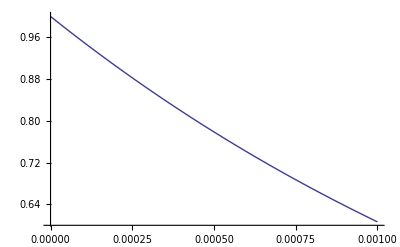

```mathematica
Plot[ⅇ^(-500x),{x,0,.001}]
```

## SVA Model

```mathematica
MassesRobot=Join[ConstantArray[0,nb-1],mm/.constsubs]
```

{0,0,3/2,5,20,5,3/2}

```mathematica
Offsets=Join[ConstantArray[0,{nb-1,3}],JointOffsetsSTT]
Coms=Join[ConstantArray[0,{nb-1,3}],ComOffsetsSTT]
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 1/2
0 | 0 | 1/2
0 | (p(1))/4 | 0
0 | 0 | -1/2
0 | 0 | -1/2)

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 3/8
0 | 0 | 7/40
0 | (p(1))/8 | 3/40
0 | 0 | -13/40
0 | 0 | -1/8)

```mathematica
MakeEffMap[name_?StringQ,linkNumber_?IntegerQ/;0<linkNumber≤nl,linkName_?StringQ,offset_?VectorQ]:=
{
"name"->name,
"dof"->linkNumber-1,
"link"->linkName,
"offset"->offset
}
```

```mathematica
effYAML={
{"stf","SFoot",1},
{"nsf","NSFoot",nl}
}
```

(stf | SFoot | 1
nsf | NSFoot | 5)

```mathematica
ParentOriginsSTT=Join[{{0,0,0}},JointOriginsSTT,1];
```

```mathematica
effMap=(MakeEffMap[#1⟦1⟧,#1⟦3⟧,#1⟦2⟧,EffOriginsFoot⟦EffLabelMap[#1⟦1⟧]⟧-ParentOriginsSTT⟦#1⟦3⟧⟧//N]&)/@effYAML
```

{{name→stf,dof→0,link→SFoot,offset→{0.,0.,0.}},{name→nsf,dof→4,link→NSFoot,offset→{0.,0.,-0.5}}}

```mathematica
left={
"coms"->Coms,
"offsets"->ConstantArray[0,{ne,3}],
"preOffsets"->Offsets,
"inertias"->ConstantArray[0,{ne,3,3}],
"extras"->effMap
}/.p[1]->-1//N;
```

```mathematica
right={
"coms"->Coms,
"offsets"->ConstantArray[0,{ne,3}],
"preOffsets"->Offsets,
"inertias"->ConstantArray[0,{ne,3,3}],
"extras"->effMap
}/.p[1]->+1//N;
```

```mathematica
svaModel={
"name"->"3dFoot-amberx",
"nBaseDof"->nb,
"extDof"->TwistAxesExt,
"aniplotNames"->{},
"closedFormJacobianNames"->{},
"sva"->{
"parentDofs"->Range[ne]-1,
"masses"->MassesRobot//N,
"left"->left,
"right"->right
}
}
```

{name→3dFoot-amberx,nBaseDof→3,extDof→{Px,Pz,Ry,-Ry,-Ry,-Ry,Ry,Ry,Ry},aniplotNames→{},closedFormJacobianNames→{},sva→{parentDofs→{0,1,2,3,4,5,6},masses→{0.,0.,1.5,5.,20.,5.,1.5},left→{coms→(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.375
0. | 0. | 0.175
0. | -0.125 | 0.075
0. | 0. | -0.325
0. | 0. | -0.125),offsets→(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.),preOffsets→(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.5
0. | 0. | 0.5
0. | -0.25 | 0.
0. | 0. | -0.5
0. | 0. | -0.5),inertias→({0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}),extras→{{name→stf,dof→0.,link→SFoot,offset→{0.,0.,0.}},{name→nsf,dof→4.,link→NSFoot,offset→{0.,0.,-0.5}}}},right→{coms→(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.375
0. | 0. | 0.175
0. | 0.125 | 0.075
0. | 0. | -0.325
0. | 0. | -0.125),offsets→(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.),preOffsets→(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.5
0. | 0. | 0.5
0. | 0.25 | 0.
0. | 0. | -0.5
0. | 0. | -0.5),inertias→({0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}
{0.,0.,0.} | {0.,0.,0.} | {0.,0.,0.}),extras→{{name→stf,dof→0.,link→SFoot,offset→{0.,0.,0.}},{name→nsf,dof→4.,link→NSFoot,offset→{0.,0.,-0.5}}}}}}

```mathematica
YamlWriteFile[svaModel,FileNameJoin[{builddir,"sva-ambersuite.yaml"}]]
```

/home/rsinnet/Documents/MATLAB/kneefoot3d-sva-v33/build_old-model-2d-point-feet-amber-suite/sva-ambersuite.yaml

### COMPAT: Old form of SVA

```mathematica
leftx={"offsets"->Offsets,"comOffsets"->Coms}/.p[1]->-1//N;
rightx={"offsets"->Offsets,"comOffsets"->Coms}/.p[1]->+1//N;
```

```mathematica
svaModelx={
"nBaseDof"->nb,
"extDof"->TwistAxesExt,
"masses"->MassesRobot//N,
"parentDofs"->Range[ne]-1,
"left"->leftx,
"right"->rightx
}
```

{nBaseDof→3,extDof→{Px,Pz,Ry,-Ry,-Ry,-Ry,Ry,Ry,Ry},masses→{0.,0.,1.5,5.,20.,5.,1.5},parentDofs→{0,1,2,3,4,5,6},left→{offsets→(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.5
0. | 0. | 0.5
0. | -0.25 | 0.
0. | 0. | -0.5
0. | 0. | -0.5),comOffsets→(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.375
0. | 0. | 0.175
0. | -0.125 | 0.075
0. | 0. | -0.325
0. | 0. | -0.125)},right→{offsets→(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.5
0. | 0. | 0.5
0. | 0.25 | 0.
0. | 0. | -0.5
0. | 0. | -0.5),comOffsets→(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.375
0. | 0. | 0.175
0. | 0.125 | 0.075
0. | 0. | -0.325
0. | 0. | -0.125)}}

```mathematica
YamlWriteFile[svaModelx,FileNameJoin[{builddir,"sva.yaml"}]]
```

/home/rsinnet/Documents/MATLAB/kneefoot3d-sva-v33/build_old-model-2d-point-feet-amber-suite/sva.yaml

## Conversion to MATLAB

```mathematica
Run["perl "<>FileNameJoin[{utildir,"math2mat.pl"}]<>" "<>builddir<>" "<>builddir]
```

0

```mathematica
dl2=DateString[]
```

Thu 27 Mar 2014 09:26:18

```mathematica
Print["Computation time:      "<>ToString[DateDifference[dl1,dl2,"Second"]//First]<>" seconds"];
```

Computation time:      17. seconds

## Conversion to CPP

```mathematica
Clear[getCFormNoPowers];
getCFormNoPowers[expr_]:=Module[{times},Apply[Function[code,Hold[CForm[code]],HoldAll],Hold[#]&[expr/.x_Symbol^y_Integer/;3>y>1:>times@@Table[x,{y}]]/.times->Times]];
```

```mathematica
(*Ccform=String[HoldForm@@getCFormNoPowers[Flatten[Cαζ]/.Ζxsubs/.Cstatesubs]];*)
```

```mathematica
Cstatesubs=Join[
(Q⟦#+1⟧->HoldForm@q⟦#⟧&/@(Range[ne]-1)),
(dQ⟦#+1⟧->HoldForm@dq⟦#⟧&/@(Range[ne]-1)),
(p[#+1]->HoldForm@p⟦#⟧&/@(Range[np]-1))
]
```

{p_x(t)→q⟦0⟧,p_z(t)→q⟦1⟧,q_y(t)→q⟦2⟧,q_1(t)→q⟦3⟧,q_2(t)→q⟦4⟧,q_3(t)→q⟦5⟧,q_4(t)→q⟦6⟧,p_x'(t)→dq⟦0⟧,p_z'(t)→dq⟦1⟧,q_y'(t)→dq⟦2⟧,q_1'(t)→dq⟦3⟧,q_2'(t)→dq⟦4⟧,q_3'(t)→dq⟦5⟧,q_4'(t)→dq⟦6⟧,p(1)→p⟦0⟧}

```mathematica
ToCForm[expr_?MatrixQ]:=Flatten@(exprᵀ)/.Ζxsubs/.Cstatesubs;
ToCForm[expr_?VectorQ[expr]]:=expr/.Ζxsubs/.Cstatesubs;
ToCForm[expr_/;!ListQ[expr]]:=Flatten@expr/.Ζxsubs/.Cstatesubs;
```

```mathematica
DDfχz=ParallelSimplify[DDfχ/.Ζsubs];
(*WriteExprζ[DDfχz,"DM1Dqzmat"];*)
```

```mathematica
plotposcform=ToCForm@ppζ;
hnsfcform=ToCForm@pnsf⟦3⟧;
```

#### Splice code into templates

```mathematica
MakeCpp[file_?StringQ]:=
Splice[FileNameJoin[{nbdir,"templates",file<>".mcc"}],FileNameJoin[{builddir,file<>".cc"}]]
```

```mathematica
MakeCpp["PlotPositions"];
MakeCpp["HeightNSF"];
```